## Bifurcation condition for localised bulging of an inflated membrane tube

Prepared by Yibin Fu (y.fu@keele.ac.uk) for the advanced summer schools 2022 at CISM

Solutions to exercises 3 & 4 in the lecture notes of Yibin Fu

### Exercise 3: Expression of ω(λ_1,λ_2)

```mathematica
P=(Derivative[1,0][W][r∞,z∞])/(r∞ z∞);   Force=Derivative[0,1][W][r∞,z∞]-(r∞ Derivative[1,0][W][r∞,z∞])/(2*z∞);   (*eqn (3.4)*)
f[x_, y_]:=W[x, y]-y D[W[x,y],y]-C1;     (* this is the second integral in (3.7)   *)
g[x_, y_]:=(y/D[W[x,y],y])*(C2+P x^2/2);  (* g=z'[Z] by solving Subscript[(3.7), 1]   *)
fc1=f[x, y]/.{x->r∞+e, y->z∞+d1 e+d2 e^2+d3 e^3+d4 e^4};
fc2=g[x, y]/.{x->r∞+e, y->z∞+d1 e+d2 e^2+d3 e^3+d4 e^4};

C1=C1/.Solve[(fc1/.e->0)==0, C1][[1]];   (* C1 and C2 are determined by conditions at infinity *)
C2=C2/.Solve[(z∞-fc2/.e->0)==0, C2][[1]];

yderivative=Simplify[Normal[Series[(z∞+d1 e+d2 e^2+d3 e^3)^2-(z∞+d1 e+g2 e^2/2+g3 e^3/6+g4 e^4/24)^2, {e,0,4}]]];
(* The above is actually y' squared. We assume that λ1=r∞+e; λ2=z∞+d1 e+d2 e^2+d3 e^3; z'=Subscript[z, ∞]+d1 e+g2 e^2/2+g3 e^3/6 *)
omega=Coefficient[yderivative,e^2]; gamm=Coefficient[yderivative,e^3]; α=Coefficient[yderivative,e^4];
(* (y')^2=omega y^2+gamm y^3+α y^4,     y=e  *)
(* By equating the coefficients of like powers of e in f(x, y)=0, we find d1, d2, etc *)
subd1=Solve[(D[fc1,e]/.e->0)==0, d1][[1]];
subd2=Simplify[Solve[(D[fc1,e,e]/.e->0)==0, d2][[1]]/.subd1];
subd3=Simplify[Simplify[Solve[(D[fc1,e,e,e]/.e->0)==0, d3][[1]]/.subd1]/.subd2];
subd4=Simplify[Simplify[Solve[(D[fc1,e,e,e,e]/.e->0)==0, d4][[1]]/.subd1]/.subd2/.subd3];
(*expanding the RHS of z'=g(x, y) to obtain g2, g3, etc *)
g1=Simplify[D[fc2,e]/.e->0];
g2=Simplify[D[fc2,e,e]/.e->0];
g3=Simplify[D[fc2,e,e,e]/.e->0];
g3=Simplify[D[fc2,e,e,e]/.e->0];
g4=Simplify[D[fc2,e,e,e,e]/.e->0];
d1=d1/.subd1;d2=d2/.subd2;d3=d3/.subd3;
d4=d4/.subd4;
bifcon=Simplify[omega]
```

(-((W^(1,0)[r∞,z∞]-z∞ W^(1,1)[r∞,z∞])^2)/(W^(0,2)[r∞,z∞])+((z∞)^2 (-W^(1,0)[r∞,z∞]+r∞ W^(2,0)[r∞,z∞]))/(r∞))/(z∞ W^(0,1)[r∞,z∞])

```mathematica
subwws={Derivative[0,1][W][r∞,z∞]->W2,Derivative[1,0][W][r∞,z∞]->W1,Derivative[2,0][W][r∞,z∞]->W11, Derivative[1,1][W][r∞,z∞]->W12, Derivative[0,2][W][r∞,z∞]->W22};
```

```mathematica
bifconss=Simplify[bifcon/.subwws]
```

(((-W1+r∞ W11) (z∞)^2)/(r∞)-(W1-W12 z∞)^2/W22)/(W2 z∞)

```mathematica
check=Simplify[(W22 (-W1+r∞ W11) (z∞)^2-r∞ (W1-W12 z∞)^2)/(r∞ z∞ W2 W22)-bifconss]
```

0

### Exercise 4: Equivalence between ω(λ_1,λ_2) =0 and the Jacobian=0

```mathematica
jacobian=Simplify[D[P,r∞] D[Force,z∞]-D[P,z∞] D[Force,r∞]]
```

(-r∞ (W^(1,0)[r∞,z∞]-z∞ W^(1,1)[r∞,z∞])^2+(z∞)^2 W^(0,2)[r∞,z∞] (-W^(1,0)[r∞,z∞]+r∞ W^(2,0)[r∞,z∞]))/((r∞)^2 (z∞)^3)

```mathematica
Simplify[bifcon/jacobian]
```

(r∞ (z∞)^2)/(W^(0,1)[r∞,z∞] W^(0,2)[r∞,z∞])

### Eqns (3.16)

```mathematica
P=(Derivative[1,0][W][x,y])/(x y); Force=Derivative[0,1][W][x,y]-(x Derivative[1,0][W][x,y])/(2*y);
```

```mathematica
(*If Force is fixed, y is viewed as a function of x, and we may differentiate Force to obtain dy/dx *)
```

```mathematica
dydx=dydx/.Solve[D[Force,x]+D[Force,y]*dydx==0,dydx][[1]]
```

-(y (-W^(1,0)[x,y]+2 y W^(1,1)[x,y]-x W^(2,0)[x,y]))/(2 y^2 W^(0,2)[x,y]+x W^(1,0)[x,y]-x y W^(1,1)[x,y])

```mathematica
(*The volume ration v=r^2 z'=x^2 y *)
```

```mathematica
dvdx=2 x y+x^2 dydx  (* dv/dx*)
```

2 x y-(x^2 y (-W^(1,0)[x,y]+2 y W^(1,1)[x,y]-x W^(2,0)[x,y]))/(2 y^2 W^(0,2)[x,y]+x W^(1,0)[x,y]-x y W^(1,1)[x,y])

```mathematica
dpdx=Simplify[D[P,x]+D[P,y] dydx]  (*dp/dx *)
```

(2 (x (W^(1,0)[x,y]-y W^(1,1)[x,y])^2+y^2 W^(0,2)[x,y] (W^(1,0)[x,y]-x W^(2,0)[x,y])))/(x^2 y (-2 y^2 W^(0,2)[x,y]-x W^(1,0)[x,y]+x y W^(1,1)[x,y]))

```mathematica
dpdv=Simplify[dpdx/dvdx]  (* dp/dv *)
```

-(2 (x (W^(1,0)[x,y]-y W^(1,1)[x,y])^2+y^2 W^(0,2)[x,y] (W^(1,0)[x,y]-x W^(2,0)[x,y])))/(x^3 y^2 (4 y^2 W^(0,2)[x,y]+x (3 W^(1,0)[x,y]-4 y W^(1,1)[x,y]+x W^(2,0)[x,y])))

```mathematica
subwws={Derivative[0,1][W][x,y]->W2,Derivative[1,0][W][x, y]->W1,Derivative[2,0][W][x, y]->W11, Derivative[1,1][W][x, y]->W12, Derivative[0,2][W][x, y]->W22};
```

```mathematica
dpdx=dpdx/.subwws/.{x->r∞, y->z∞}
```

(2 ((W1-r∞ W11) W22 (z∞)^2+r∞ (W1-W12 z∞)^2))/((r∞)^2 z∞ (-r∞ W1+r∞ W12 z∞-2 W22 (z∞)^2))

```mathematica
dpdv=dpdv/.subwws/.{x->r∞, y->z∞}
```

-(2 ((W1-r∞ W11) W22 (z∞)^2+r∞ (W1-W12 z∞)^2))/((r∞)^3 (z∞)^2 (4 W22 (z∞)^2+r∞ (3 W1+r∞ W11-4 W12 z∞)))

```mathematica
Simplify[dpdv/bifconss]
```

```mathematica
(2 W2 W22)/((r∞)^2 z∞ (3 r∞ W1+(r∞)^2 W11-4 r∞ W12 z∞+4 W22 (z∞)^2))
```

```mathematica
Simplify[dpdx/bifconss]
```

(2 W2 W22)/(r∞ (2 W22 (z∞)^2+r∞ (W1-W12 z∞)))

This means that  dP/(d x)=ω (r∞)*(2 W2 W22)/(r∞ (2 W22 (z∞)^2+r∞ (W1-W12 z∞))), and ω (r∞)=0 iff dP/(d x)=0.

### Graphical illustrations

```mathematica
Gent97sub={W->Function[{x,y},-1/2 * (972/10) Log[1-(x^2+y^2+x^-2 y^-2-3)/(972/10)]]};
```

```mathematica
bif=Numerator[Simplify[jacobian/.Gent97sub]]
```

-236196 (-5-15 (r∞)^8 (z∞)^4+5 (r∞)^12 (z∞)^6-9 (r∞)^2 (z∞)^2 (-167+5 (z∞)^2)-6 (r∞)^6 (z∞)^4 (-501+25 (z∞)^2)+(r∞)^10 (z∞)^6 (-501+35 (z∞)^2)+(r∞)^4 (z∞)^2 (-25+2004 (z∞)^4+20 (z∞)^6))

```mathematica
nn=Simplify[Force/.Gent97sub]
```

(243 (1+(r∞)^4 (z∞)^2-2 (r∞)^2 (z∞)^4))/(z∞ (5+5 (r∞)^4 (z∞)^2+(r∞)^2 (z∞)^2 (-501+5 (z∞)^2)))

```mathematica
zf[r∞_]=z∞/.Solve[nn==0, z∞][[4]]
```

1/2 √((r∞)^2+(√(8+(r∞)^6))/(r∞))

```mathematica
SetDirectory["C:\\Users\\Yibin Fu\\OneDrive - University of Keele\\TJU\\conferences\\CISM"]
```

C:\Users\Yibin Fu\OneDrive - University of Keele\TJU\conferences\CISM

```mathematica
bifcongent=bifcon/.Gent97sub;
Dbifcongent=D[bifcongent,r∞];
subTangentWithZ=FindRoot[{bifcongent==0,Dbifcongent==0},{r∞,2},{z∞,3.5}]
```

{r∞→2.50501,z∞→3.61985}

```mathematica
rinf1=r∞/.FindRoot[(bifcongent/.z∞->1.01)==0,{r∞,2}]
```

1.68466

```mathematica
rinf2=r∞/.FindRoot[(bifcongent/.z∞->1.01)==0,{r∞,9}]
```

9.64499

```mathematica
data1={{rinf1,1.01}};
Do[zinf=1.01+(3.619-1.01)*k/500; rinf1=r∞/.FindRoot[(bifcongent/.z∞->zinf)==0,{r∞, rinf1}][[1]]; data1=Append[data1,{rinf1,zinf}],{k,1,500}]; data1=Append[data1,{2.505013358071,3.6198524619081}];

data2={{rinf2,1.01}};
Do[zinf=1.01+(3.619-1.01)*k/500; rinf2=r∞/.FindRoot[(bifcongent/.z∞->zinf)==0,{r∞, rinf2}][[1]]; data2=Append[data2,{rinf2,zinf}],{k,1,500}]; 

data=Join[data1,Reverse[data2]];
```

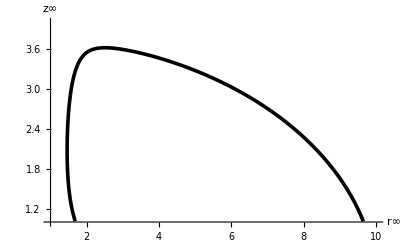

```mathematica
fig1=ListPlot[data,Joined->True, PlotRange->{{1,10},{1,4}},PlotStyle->{{Black,Thickness[0.0065]}},AxesLabel->{Style["r∞",FontSize->22,FontColor->Black,FontFamily->"Cambria Math"],Style["z∞",FontSize->22,FontColor->Black,FontFamily->"Cambria"]},AxesStyle->{Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.005],Arrowheads[{0,0.05}]]},TicksStyle->Directive[Black,14]]
```

```mathematica
gus1=r∞/.FindRoot[(nn/.{z∞->4})==0,{r∞,1}]
```

5.65668

```mathematica
gus10=z∞/.FindRoot[(nn/.{r∞->1.01})==0,{z∞,1}]
```

1.00007

```mathematica
gus2=r∞/.FindRoot[(3.48-nn/.{z∞->4})==0,{r∞,1}]
```

3.32296

```mathematica
gus20=z∞/.FindRoot[(3.48-nn/.{r∞->1.01})==0,{z∞,1}]
```

3.32007

```mathematica
dataL1={}; dataL2={};
```

```mathematica
Do[rr=1.01+(gus1-1.01)*k/100; zz=z∞/.FindRoot[(nn/.{r∞->rr})==0,{z∞,3}]; dataL1=Append[dataL1, {rr, zz}],{k,1,99}];
```

```mathematica
Do[rr=1.01+(gus2-1.01)*k/100; zz=z∞/.FindRoot[(3.48-nn/.{r∞->rr})==0,{z∞,3}]; dataL2=Append[dataL2, {rr, zz}],{k,1,99}];
```

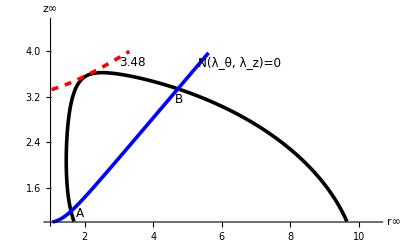

```mathematica
fig1=ListPlot[{data,dataL1,dataL2} ,Joined->True, PlotRange->{{1,10.5},{1,4.5}},PlotStyle->{{Black,Thickness[0.0065]},{Blue,Thickness[0.0065]},{Red,Dashed,Thickness[0.0065]}},AxesLabel->{Style["r∞",FontSize->22,FontColor->Black,FontFamily->"Cambria Math"],Style["z∞",FontSize->22,FontColor->Black,FontFamily->"Cambria"]},AxesStyle->{Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.005],Arrowheads[{0,0.05}]]},TicksStyle->Directive[Black,14],Epilog->{{Text[Style["N(λ_θ, λ_z)=0",FontSize->12,FontFamily->"Cambria Math"],{6.5,3.8}]},{Text[Style["3.48",FontSize->12,FontFamily->"Cambria Math"],{3.4,3.8}]},{Text[Style["A",FontSize->12,FontFamily->"Cambria Math"],{1.85,1.15}]},{Text[Style["B",FontSize->12,FontFamily->"Cambria Math"],{4.75,3.15}]}} ]
```

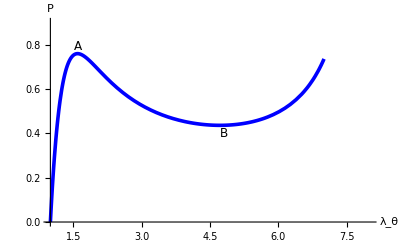

```mathematica
fig2=Plot[P/.Gent97sub/.z∞->zf[r∞],{r∞,1,7},PlotRange->{{1,8},{0,0.9}},PlotStyle->{{Blue, Thickness[0.0065]},{Blue,Dashed,Thickness[0.0065]},{Dotted,Thickness[0.0065]}},AxesLabel->{Style["λ_θ",FontSize->22,FontColor->Black,FontFamily->"Cambria Math"],Style["P",FontSize->22,FontColor->Black,FontFamily->"Cambria"]},AxesStyle->{Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.005],Arrowheads[{0,0.05}]]},TicksStyle->Directive[Black,14] ,AxesStyle->Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]],Epilog->{{Text[Style["A",FontSize->12,FontFamily->"Cambria Math"],{1.6,0.79}]},{Text[Style["B",FontSize->12,FontFamily->"Cambria Math"],{4.8,0.4}]}}]
```

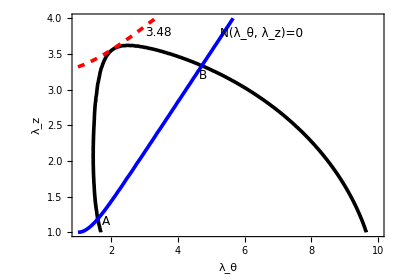

```mathematica
fig1=ContourPlot[{bif==0,nn==0,nn==3.48},{r∞,1,10},{z∞,1,4}, AspectRatio->0.7,Frame->{True, True, False,False},ContourStyle->{{Black, Thickness[0.0065]},{Blue,Thickness[0.0065]},{Red,Dashed,Thickness[0.0065]}},FrameLabel->{Style["λ_θ",FontSize->20,FontColor->Black,FontFamily->"Cambria Math"],Style["λ_z",FontSize->20,FontColor->Black,FontFamily->"Cambria"]},FrameStyle->Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]],TicksStyle->Directive[Black,18],FrameStyle->Black,Epilog->{{Text[Style["N(λ_θ, λ_z)=0",FontSize->12,FontFamily->"Cambria Math"],{6.5,3.8}]},{Text[Style["3.48",FontSize->12,FontFamily->"Cambria Math"],{3.4,3.8}]},{Text[Style["A",FontSize->12,FontFamily->"Cambria Math"],{1.85,1.15}]},{Text[Style["B",FontSize->12,FontFamily->"Cambria Math"],{4.75,3.2}]}} ]
```

```mathematica
pressureGent=(D[W[x,y],x]/.{x->r∞, y->z∞})/(r∞*z∞)/.Gent97sub;
```

```mathematica
data10=Join[Table[{ data1[[k,2]],pressureGent/.{r∞->data1[[k,1]],z∞->data1[[k,2]]}},{k,1,Dimensions[data1][[1]]}],Reverse[Table[{ data2[[k,2]],pressureGent/.{r∞->data2[[k,1]],z∞->data2[[k,2]]}},{k,1,Dimensions[data2][[1]]}]]];
```

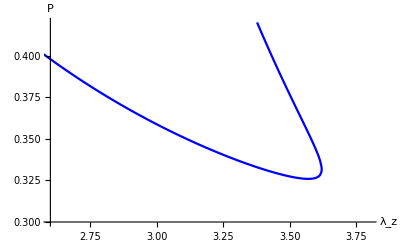

```mathematica
fig7a=ListPlot[{data10},Joined->True,PlotRange->{{2.6,3.8},{0.3,0.42}},PlotStyle->{{PointSize[0.015], Blue},{PointSize[0.015], Black, Dashed}}, AxesStyle->{Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.005],Arrowheads[{0,0.05}]]},AxesLabel->{Style["λ_z",FontSize->20,FontFamily->"Times New Roman"],Style["P",FontSize->20,FontFamily->"Times New Roman"]},Epilog->{Text[Style[ "Gent model",Medium],{4,2}]}]
```

```mathematica
forceGent=Force/.Gent97sub;
```

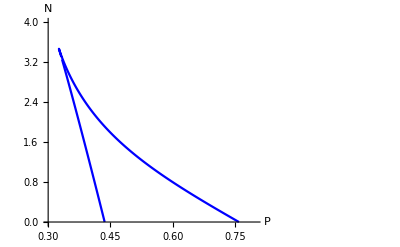

```mathematica
fig7b=ListPlot[{Table[{ pressureGent/.{r∞->data1[[k,1]],z∞->data1[[k,2]]},forceGent/.{r∞->data1[[k,1]],z∞->data1[[k,2]]}},{k,1,Dimensions[data1][[1]]}],Table[{ pressureGent/.{r∞->data2[[k,1]],z∞->data2[[k,2]]},forceGent/.{r∞->data2[[k,1]],z∞->data2[[k,2]]}},{k,1,Dimensions[data2][[1]]}]},Joined->True,PlotStyle->{{PointSize[0.015], Blue},{PointSize[0.015], Blue}}, PlotRange->{{0.3,0.8},{0,4}},AxesStyle->{Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.005],Arrowheads[{0,0.05}]]},AxesLabel->{Style["P",FontSize->20,FontFamily->"Times New Roman"],Style["N",FontSize->20,FontFamily->"Times New Roman"]},Epilog->{Text[Style[ "Gent model",Medium],{4,2}]}]
```